```mathematica
AppendTo[$Path,"C:\\Users\\Nilo\\__DATA\\Mega\\DATA\\eclipse-workspace\\Geometry"];
<<Geometry`
```

## TEST1

### Case 1

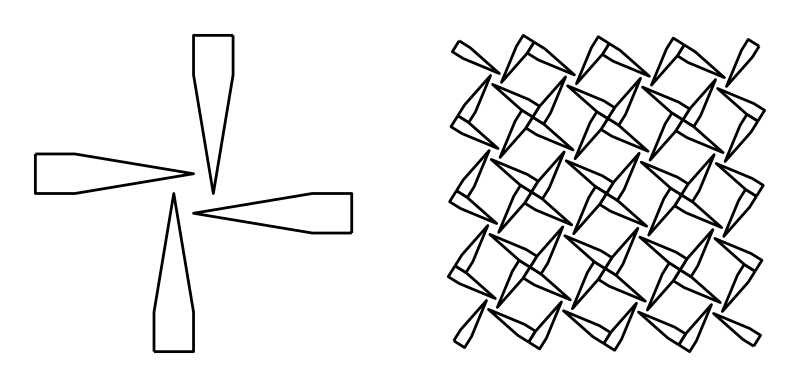

```mathematica
teil[figke_]:= Module[{rotp},
rotp=2mid[figke];
{figke,rot3[figke,{π/2,rotp}],rot3[figke,{π,rotp}],rot3[figke,{3 π /2,rotp}]}]

dpoly:=tra3[newGeo[8],{2,1}]
dpoly:={tra3[newGeo[10,RGBColor[1,.85,.95,.1]][[1]],{1,1}],{Red,1,.005,2 π,2 π}}
dpoly:={{{1,{{0,0},{1,0},{1,1},{.5,4.0},{0,1}}},{White,1}},{Black,1,.005,2 π,2 π}}
GraphicsRow[{Graphics[Nest[teil,dpoly,1]//toGL],
Graphics[rot3[Nest[teil,dpoly,3],{58Degree,{0,0}}]//toGL]}]
```

### Case 2

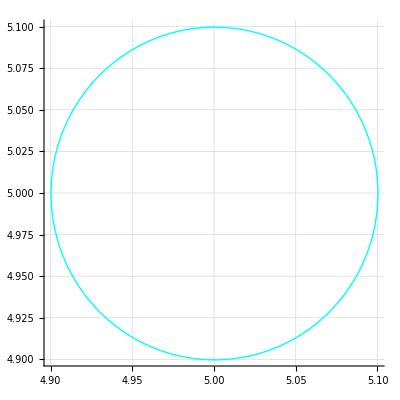

```mathematica
cCircle[{5,5},.1]//toGL//gr1
```

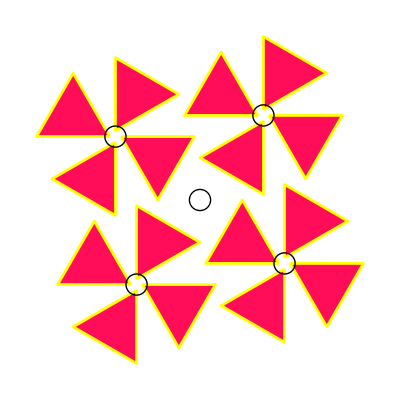

```mathematica
teil[figke_]:= Module[{rotp},
rotp=2mid[figke];
{figke,rot3[figke,{π/2,rotp}],rot3[figke,{π,rotp}],rot3[figke,{3 π /2,rotp}],
repCol[cCircle[rotp,.25],{Black}]
}]
dpoly:={{{1,{{4,0},{4,5},{2,5},{2,4}}},{LightGreen,1}},{Green,1,.005,2 π,2 π}}
dpoly:={tra3[newGeo[3,RGBColor[1,.05,.35,.1]][[1]],{1,1}],{Yellow,1,.005,2 π,2 π}}
Nest[teil,dpoly,2]//toGL//gr
```

### Case 3

```mathematica
ind:=Tuples[Composition@@{sym4ref,sym4rot},3]
```

```mathematica
dpoly:={{{1,{{0,0},{0.5,0.2},{1,1},{0.2,0.9}}},{RGBColor[1, 0.9500000000000001, 0],1}},{RGBColor[0.06, 0.06, 0.06],1,0.005,2 π,2 π}}
dpoly:={{{1,{{0,0},{1,0},{0.7,1},{0.3,1}}},{RGBColor[0.87, 0.87, 0.87, 0.9],1}},{RGBColor[0.06, 0.06, 0.06],1,0.005,2 π,2 π}}
dpoly:={{{1,{{0,0},{0.25,0},{0.5,0.25},{0.5,.5}}},{RGBColor[0.87, 0.87, 0.87, 0.9],1}},{RGBColor[0.06, 0.06, 0.06],1,0.005,2 π,2 π}}
sym4rot[sym4ref[dpoly]]//toGL//gr1
```

-Graphics-

```mathematica
Table[ind[[k]][dpoly]//toGL//gr,{k,1,Length[ind]}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

### Case 4 ( IN-DEVELOPMENT )

```mathematica
dpoly0:={{{1,{{0.25,0.0},{0.5,0.0},{0.5,0.75},{0.75,0.75},{0.75,1.0},{0.0,1.0},{0.0,0.75},{0.25,0.75}}},{Cyan,1}},{RGBColor[0.06, 0.06, 0.06],1,0.005,2 π,2 π}}
dpolyA:={{{1,{{0.5,0},{1,0.5},{1,1},{0.5,0.5},{0,1},{0,.5}}},{RGBColor[0.87, 0.87, 0.87, 0.9],1}},{RGBColor[0.06, 0.06, 0.06],1,0.005,2 π,2 π}}
dpolyB:={{{1,{{0,0},{0.5,0},{0,0.5}}},{Cyan,1}},{RGBColor[0.06, 0.06, 0.06],1,0.005,2 π,2 π}}
dpolyC:={{{1,{{0.5,0},{1,0},{1,0.5}}},{Cyan,1}},{RGBColor[0.06, 0.06, 0.06],1,0.005,2 π,2 π}}
dpoly:={dpolyA,dpolyB,dpolyC}
dpoly//toGL//gr1;
sym4ovr1[dpoly]//toGL//gr1
```

-Graphics-

```mathematica
sym4ovr1[figke_]:=Module[{rotp},
rotp={1,1};
tra3[Scale[
{
figke,
rot3[ref3[figke,{{1,0},rotp}],{π,{1.5,0.5}}],
tra3[figke,{1,1}],
tra3[rot3[ref3[figke,{{1,0},rotp}],{π,{1.5,0.5}}],{-1,1}]
},
.5],{-.5,-.5}]]
```

```mathematica
ind:=Tuples[Composition@@{sym4rot,sym4ref,sym4ovr1},3]
Table[ind[[k]][dpoly]//toGL//gr,{k,1,Length[ind]}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
ind//TableForm
```

sym4rot@*sym4rot@*sym4rot
sym4rot@*sym4rot@*sym4ref
sym4rot@*sym4rot@*sym4ovr1
sym4rot@*sym4ref@*sym4rot
sym4rot@*sym4ref@*sym4ref
sym4rot@*sym4ref@*sym4ovr1
sym4rot@*sym4ovr1@*sym4rot
sym4rot@*sym4ovr1@*sym4ref
sym4rot@*sym4ovr1@*sym4ovr1
sym4ref@*sym4rot@*sym4rot
sym4ref@*sym4rot@*sym4ref
sym4ref@*sym4rot@*sym4ovr1
sym4ref@*sym4ref@*sym4rot
sym4ref@*sym4ref@*sym4ref
sym4ref@*sym4ref@*sym4ovr1
sym4ref@*sym4ovr1@*sym4rot
sym4ref@*sym4ovr1@*sym4ref
sym4ref@*sym4ovr1@*sym4ovr1
sym4ovr1@*sym4rot@*sym4rot
sym4ovr1@*sym4rot@*sym4ref
sym4ovr1@*sym4rot@*sym4ovr1
sym4ovr1@*sym4ref@*sym4rot
sym4ovr1@*sym4ref@*sym4ref
sym4ovr1@*sym4ref@*sym4ovr1
sym4ovr1@*sym4ovr1@*sym4rot
sym4ovr1@*sym4ovr1@*sym4ref
sym4ovr1@*sym4ovr1@*sym4ovr1

## temp

```mathematica
FileNameJoin[{$InstallationDirectory,"SystemFiles","Components","AutoCompletionData","Main","OptionValues"}]
```

C:\Program Files\Wolfram Research\Mathematica\12.3.1\SystemFiles\Components\AutoCompletionData\Main\OptionValues

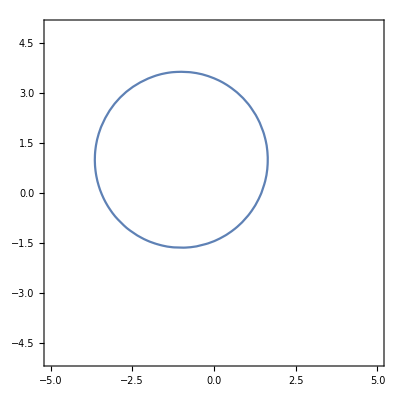

```mathematica
ClearAll[x,y]
ContourPlot[x^2+y^2+2x-2y-5==0,{x,-5,5},{y,-5,5},Axes->True]
```

```mathematica
(3z Conjugate[z]//ComplexExpand)/.z:>x+I y//Expand
```

```mathematica
z Conjugate[z]/. z-> x+I y
```

(x+ⅈ y) (Conjugate[x]-ⅈ Conjugate[y])

```mathematica
3(x+I y)(x-I y)//Expand
```

3 x^2+3 y^2

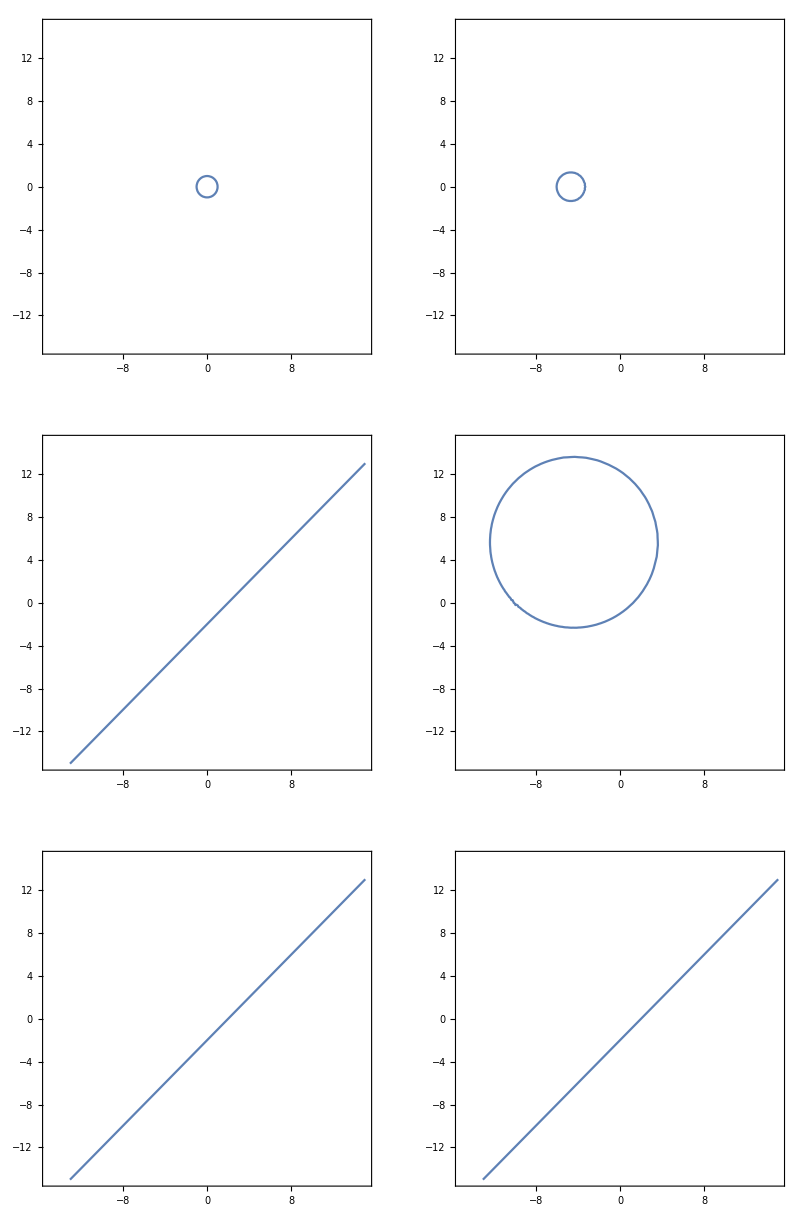

```mathematica
eqn1=ComplexExpand[z Conjugate[z]-1/.z->(1z+0)/(0z+1),z]/.{Re[z]->x,Im[z]->y};
eqn2=ComplexExpand[z Conjugate[z]-1/.z->(0.5z+1)/(1z+4),z]/.{Re[z]->x,Im[z]->y}//FullSimplify;
eqn3=ComplexExpand[Im[z]-Re[z]+2/.z->(1z+0)/(0z+1),z]/.{Re[z]->x,Im[z]->y};
eqn4=ComplexExpand[Im[z]-Re[z]+2/.z->(z+1)/(.1z+1),z]/.{Re[z]->x,Im[z]->y};
eqn5=ComplexExpand[Im[z]-Re[z]+2/.z->(z+0)/(0z+1),z]/.{Re[z]->x,Im[z]->y};
eqn6=ComplexExpand[Im[z]-Re[z]+2/.z->(z+2)/(.1z+1)/.z->(1z-2)/(-.1z+1),z]/.{Re[z]->x,Im[z]->y};

a=15;
GraphicsGrid[{
{
ContourPlot[eqn1==0,{x,-a,a},{y,-a,a},Axes->True],
ContourPlot[eqn2==0,{x,-a,a},{y,-a,a},Axes->True]},
{ContourPlot[eqn3==0,{x,-a,a},{y,-a,a},Axes->True],
ContourPlot[eqn4==0,{x,-a,a},{y,-a,a},Axes->True]},
{ContourPlot[eqn5==0,{x,-a,a},{y,-a,a},Axes->True],
ContourPlot[eqn6==0,{x,-a,a},{y,-a,a},Axes->True]
}
}]
```

```mathematica
z Conjugate[z]-1/.z->(1z-5)/(0z+5)//Expand
```

-z/5-Conjugate[z]/5+1/25 z Conjugate[z]

```mathematica
m:={{4,9},{11,25}};
t:={{1,1},{0,1}};
```

```mathematica
m//mf
m.Inverse[t]//mf
m.Inverse[t].Inverse[t]//mf
m.MatrixPower[Inverse[t],5]//mf
```

(4 | 9
11 | 25)

(4 | 5
11 | 14)

(4 | 1
11 | 3)

(4 | -11
11 | -30)

```mathematica
Clear[a,b,c,d]
ma={{a,b},{c,d}};
mt={{1,1},{0,1}};
ms={{0,-1},{1,0}};
mst={{0,-1},{1,1}};
```

```mathematica
mst.ma.Inverse[mst]//mf
```

(-c+d | -c
a-b+c-d | a+c)

```mathematica
mt.{1,0}.Inverse[mt]
```

{1,-1}

```mathematica
maa={{5,2},{-2,3}};
maa={{b+d,b},{-b,d}};
maa1={{a,-c},{c,a+c}};
{mst.maa,maa.mst}
{mst.maa1,maa1.mst}
```

{{{b,-d},{d,b+d}},{{b,-d},{d,b+d}}}

{{{-c,-a-c},{a+c,a}},{{-c,-a-c},{a+c,a}}}

```mathematica
mm={{1,0,1,-1},{0,1,1,0},{1,-1,0,-1},{1,0,1,-1}};
```

```mathematica
MatrixRank[mm]
NullSpace[mm]
RowReduce[mm]
```

2

{{1,0,0,1},{-1,-1,1,0}}

{{1,0,1,-1},{0,1,1,0},{0,0,0,0},{0,0,0,0}}

```mathematica
mm.{-1,-1,1,0}
```

{0,0,0,0}

```mathematica
maa2=a mst+b IdentityMatrix[2];
maa2=a IdentityMatrix[2] + b mst+c Inverse[mst]
mst.maa2//mf
maa2.mst//mf
```

{{a+c,-b+c},{b-c,a+b}}

(-b+c | -a-b
a+b | a+c)

(-b+c | -a-b
a+b | a+c)

```mathematica
mst//mf
Inverse[mst]//mf
```

(0 | -1
1 | 1)

(1 | 1
-1 | 0)

```mathematica
Graphics3D[{Opacity[0.6],Octahedron[],Circumsphere[Octahedron[]]}]
```

-Graphics3D-

## UZT-1

```mathematica
p1:={0,0};
p2:={3,1};
p3:={1,3};
p4:={4,3};
p5:={-2,3};
Graphics[{
Arrow[{p1,p5}],
Line[{p1,p2}],
HalfLine[{p1,p4}],
Dashed,InfiniteLine[{p1,p3}]
},
AxesOrigin->{0,0},Axes->True,AxesLabel->{"X","Y"},
PlotRange->{{-5,5},{-5,5}}]
```

-Graphics-

```mathematica
tra3cp[figs_,t_]:={figs,figs/.f:pnt:>TranslationTransform[t][f]}
```

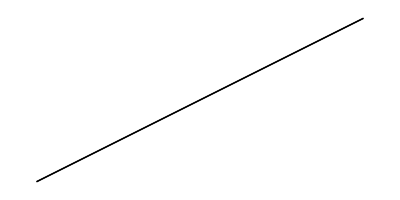

```mathematica
tra3cp[{Line[{{0,0},{4,2}}]},{0,0}]//toGL//Graphics
```

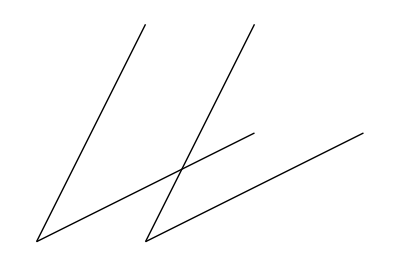

```mathematica
tra3cp[{Line[{{0,0},{4,2}}],Line[{{0,0},{2,4}}]},{-2,0}]//toGL//Graphics
```

```mathematica
trans[figke_]:= Module[{},
{
figke,
tra3cp[figke,{1,0}]
}
]
line:={Line[{{0,0},{4,2}}]}
```

```mathematica
Fold[tra3cp,line,Table[{1,1},{k,1}]]//tf
```

Line[{{0,0},{4,2}}]
Line[{{1,1},{5,3}}]

```mathematica
Fold[tra3cp,line,Table[{k,k},{k,2}]]//tf
```

Line[{{0,0},{4,2}}] | Line[{{1,1},{5,3}}]
Line[{{2,2},{6,4}}] | Line[{{3,3},{7,5}}]

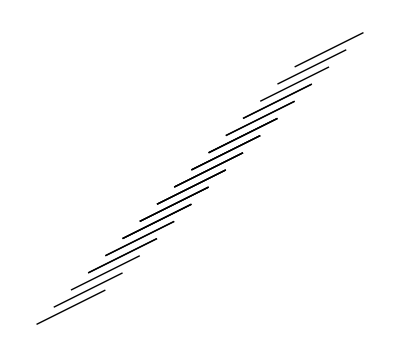

```mathematica
Fold[tra3cp,line,Table[{k,k},{k,5}]]//toGL//Graphics
```

## UZT-2

```mathematica
Table[ReIm[ⅇ^((k 2 Pi I)/4)],{k,0,3}]//tf
Table[ReIm[ⅇ^((k 2 Pi I)/8)],{k,0,7}]//tf
```

1 | 0
0 | 1
-1 | 0
0 | -1

1 | 0
1/(√2) | 1/(√2)
0 | 1
-1/(√2) | 1/(√2)
-1 | 0
-1/(√2) | -1/(√2)
0 | -1
1/(√2) | -1/(√2)

```mathematica
lines[n_]:=Map[Line[{{0,0},#}]&,Table[ReIm[ⅇ^((k 2 Pi I)/n)],{k,0,n-1}]]
{{{1,{{0,0},#}},{White,1}},{Black,1,.005,2 π,2 π}};
lines[n_]:=Map[{{{1,{{0,0},#}},{Red,1}},{Blue,1,.025,2 π,2 π}}&,Table[ReIm[ⅇ^((k 2 Pi I)/n)],{k,0,n-1}]]
```

```mathematica
GraphicsRow[{
lines[16]//toGL//Graphics,
lines[32]//toGL//Graphics
}]
```

-Graphics-

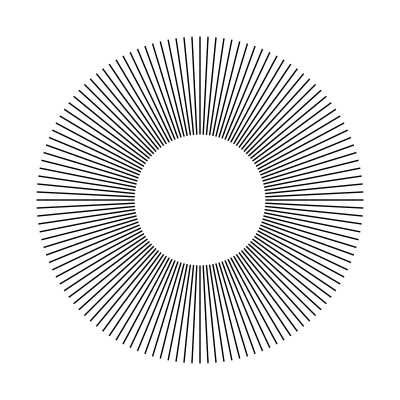

```mathematica
lines2[n_]:=Map[Line[{0.4#[[2]],#[[2]]}]&,Table[{(k+1)/n ReIm[ⅇ^((k 2 Pi I)/n)],ReIm[ⅇ^((k 2 Pi I)/n)]},{k,0,n-1}]]
lines2[128]//toGL//Graphics
```

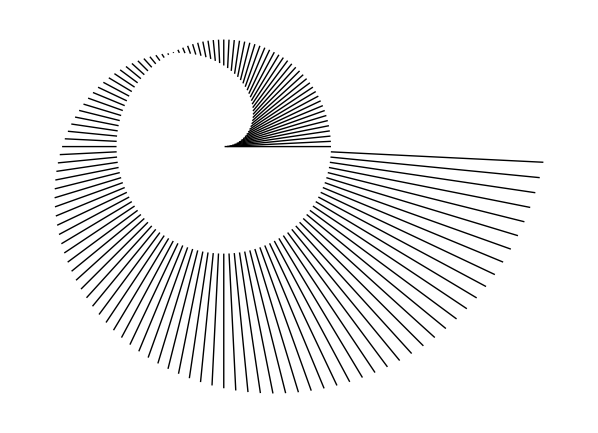

```mathematica
lines3[n_]:=Map[Line[{#[[1]],#[[2]]}]&,Table[{((3k+1)/n)ReIm[ⅇ^((k 2 Pi I)/n)],ReIm[ⅇ^((k 2 Pi I)/n)]},{k,0,n-1}]]
lines3[128]//toGL//Graphics
```

```mathematica
{{{1,{{0,0},{1,0},{1,1},{.5,4.0},{0,1}}},{White,1}},{Black,1,.005,2 π,2 π}}
```

```mathematica
RSolve[a[n,x+1]-a[n,x]==n x^(n-1),a[n,x],{n,x}]
```

{{a[n,x]→n (-HurwitzZeta[1-n,x]+Zeta[1-n])+C[1][n]}}

```mathematica
3HurwitzZeta[-2,4]+Zeta[-2]
```

-42